```mathematica
Clear["Global`*"]
```

```mathematica
g=9.81;
l = 1;
poc=1;
time = {t, 0, 10};
init = {y[0] == poc, y'[0] == 0};
rovnice = y''[t] == - g/l*Sin[y[t]];
```

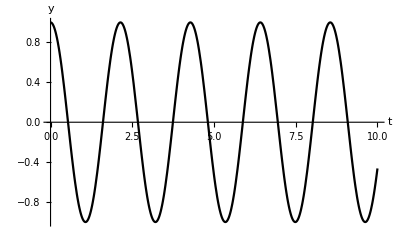

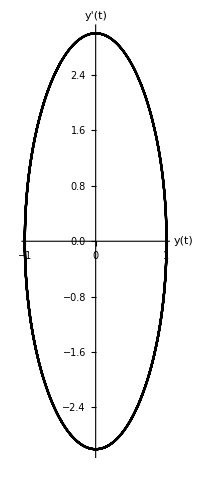

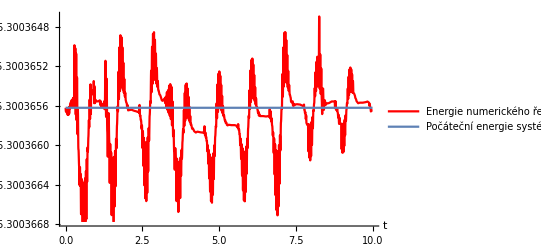

```mathematica
sol=NDSolve[{y''[t]  +g/l*Sin[y[t]]==0, y[0] == poc, y'[0] == 0}, y, time];
Plot[
Evaluate[y[t] /. sol], time,
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger],
Style[ToExpression["y",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
ParametricPlot[
Evaluate[{y[t], y'[t]}/. sol],Evaluate[time],
AxesLabel->{
Style[ToExpression["y(t)",TeXForm,HoldForm],Larger],
Style[ToExpression["y'(t)",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
p1=Plot[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. sol], time,PlotStyle->Red,PlotLegends->{"Energie numerického řešení v čase"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick,PlotLegends->{"Počáteční energie systému"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}];
Show[p1,p2,PlotRange->All]
```

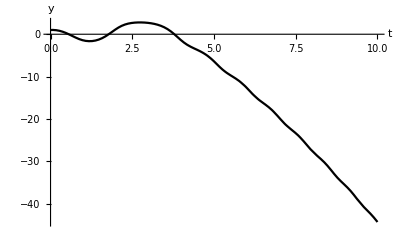

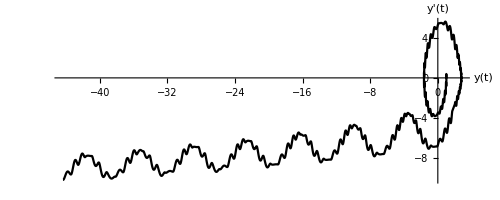

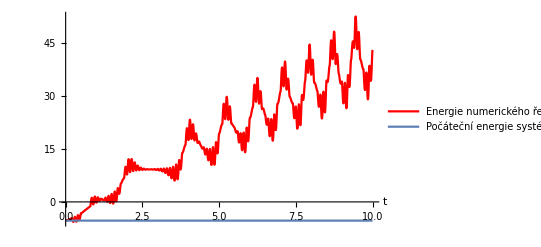

```mathematica
solEU=NDSolve[{y''[t]  +g/l*Sin[y[t]]==0, y[0] == poc, y'[0] == 0}, y, time,Method->"ExplicitEuler",StartingStepSize->0.1,MaxStepSize->0.1,MaxSteps->100];
Plot[
Evaluate[y[t] /. solEU], time,
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger],
Style[ToExpression["y",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
ParametricPlot[
Evaluate[{y[t], y'[t]}/. solEU],Evaluate[time],
AxesLabel->{
Style[ToExpression["y(t)",TeXForm,HoldForm],Larger],
Style[ToExpression["y'(t)",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
p1=Plot[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. solEU], time,PlotStyle->Red,PlotLegends->{"Energie numerického řešení v čase"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick,PlotLegends->{"Počáteční energie systému"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}];
Show[p1,p2,PlotRange->All]
```

```mathematica
H = p[t]^2/2 -g/l *Cos[q[t]];
eqs = {p'[t] == -D[H, q[t]], q'[t] == D[H, p[t]]};
ics = {p[0] == 0,q[0] == poc};
vars = {q[t], p[t]};
```

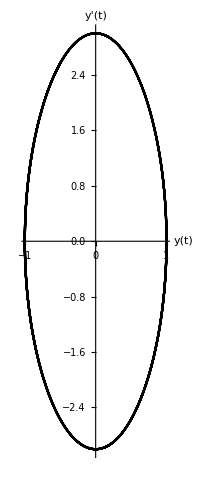

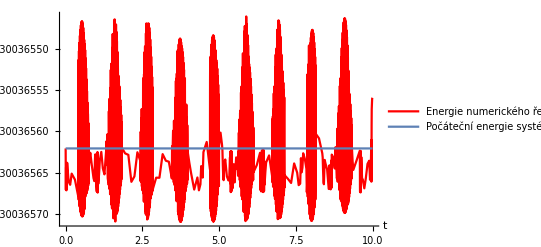

```mathematica
rese=NDSolve[{eqs,ics},vars,time,Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->4,"PositionVariables"->{q[t]}}];
ParametricPlot[
Evaluate[vars/. rese],Evaluate[time],
AxesLabel->{
Style[ToExpression["y(t)",TeXForm,HoldForm],Larger],
Style[ToExpression["y'(t)",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
p1=Plot[Evaluate[p[t]^2/2 -g/l *Cos[q[t]]/.rese], time,PlotStyle->Red,PlotLegends->{"Energie numerického řešení v čase"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick,PlotLegends->{"Počáteční energie systému"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}];
Show[p1,p2,PlotRange->All]
```

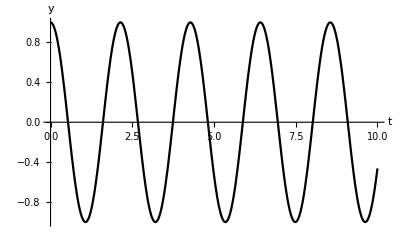

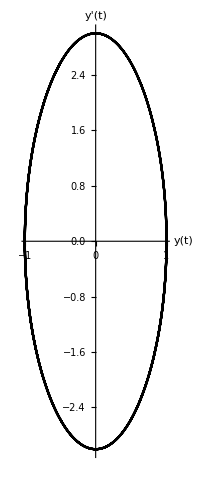

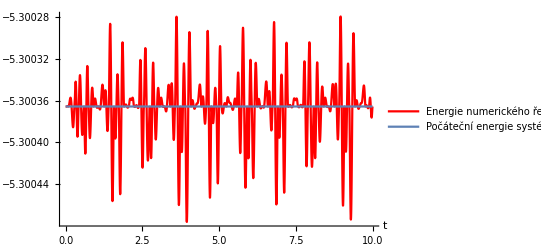

```mathematica
solP=NDSolve[{y''[t] + g/l *Sin[y[t]] == 0, y[0] == poc, y'[0] == 0}, y, time,Method->{"Projection",Method->"ExplicitRungeKutta","Invariants"->-g/l *Cos[poc]}];
Plot[
Evaluate[y[t] /. solP], time,
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger],
Style[ToExpression["y",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
ParametricPlot[
Evaluate[{y[t], y'[t]}/. solP],Evaluate[time],
AxesLabel->{
Style[ToExpression["y(t)",TeXForm,HoldForm],Larger],
Style[ToExpression["y'(t)",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
p1=Plot[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. solP], time,PlotStyle->Red,PlotLegends->{"Energie numerického řešení v čase"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick,PlotLegends->{"Počáteční energie systému"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}];
Show[p1,p2,PlotRange->All]
```

```mathematica
tabulka0=Table[t, {t,0,10, 1 }];
tabulkaA=Table[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. sol], {t,0,10, 1 }];
tabulkaB=Table[Evaluate[p[t]^2/2 -g/l *Cos[q[t]]/.rese], {t,0,10, 1 }] ;
tabulkaC=Table[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. solP], {t,0,10, 1 }];
NumberForm[Grid[{{"Čas","NDSolve","SymplecticRungeKutta","Projection"},{TableForm[tabulka0],TableForm[tabulkaA],TableForm[tabulkaB],TableForm[tabulkaC]}},Frame->All],10] //TeXForm
```

Čas | NDSolve | SymplecticRungeKutta | Projection
0
1
2
3
4
5
6
7
8
9
10 | -5.300365621
-5.300365503
-5.300365607
-5.300365352
-5.300365507
-5.300365437
-5.300365525
-5.300366032
-5.300366084
-5.300365929
-5.300365649 | -5.300365621
-5.300365669
-5.300365639
-5.300365644
-5.300365646
-5.300365575
-5.300365688
-5.300365495
-5.300365652
-5.300365615
-5.300365559 | -5.300365621
-5.300364618
-5.300365847
-5.300351305
-5.300348124
-5.300357624
-5.300343897
-5.300362859
-5.300399387
-5.300377653
-5.300365623

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------PERIODA

```mathematica
GetPeriod[g_, l_, initpos_]:=(
tend := 0;
NDSolve[{θ''[t] == - g/l*Sin[θ[t]], θ[0]==initpos, θ'[0] == 0, WhenEvent[θ[t]==0, {tend = t, "StopIntegration"}]}, θ, {t,0, 2*Pi*Sqrt[l/g] }];
4*tend
)
```

```mathematica
PeriodAsFunctionOfInitPosition = Table[{initpos, GetPeriod[g, l, initpos]}, {initpos,1/1000, Pi/2, 0.1 }]
```

{{0.001,2.00605},{0.101,2.00735},{0.201,2.01114},{0.301,2.01749},{0.401,2.02642},{0.501,2.038},{0.601,2.05231},{0.701,2.06947},{0.801,2.0896},{0.901,2.11285},{1.001,2.13942},{1.101,2.16953},{1.201,2.20344},{1.301,2.24148},{1.401,2.28401},{1.501,2.33149}}

```mathematica
PeriodaAprox[θ_] := 2*Pi*Sqrt[l/g]*(1+θ^2/16+11*θ^4/3072)
```

```mathematica
ElipInt[θ_]:=Integrate[4*Sqrt[l/g]*1/Sqrt[1-Sin[θ/2]^2*Sin[y]^2],{y,0,Pi/2}]
```